```mathematica
SetDirectory[NotebookDirectory[]];
Get["Package.m"];
loadFiles[];
```

# Rappresentazione Grafica delle Funzioni polinomiali -Graphics- >< Versione Studente ><

## a cura di

Simone Bertolini, Alessio Francesconi, Matteo Grillini

```mathematica
Hyperlink[StatusArea[Import["img/right_arrow.png"], "Introduction"],{EvaluationNotebook[], "Introduction"}]
```

## 1.1 Introduzione

la geometri e l’algebra sono due branche di quella meravigliosa materia ma come sono legate?

Le funzioni polinomiali ci permettono di notare il collegamento fra figure ed espressioni analitiche... vediamo come

```mathematica
Hyperlink[StatusArea[Import["img/right_arrow.png"], "Setup"],{EvaluationNotebook[], "Setup"}]
```

## Setup Project

Per iniziare il tutorial ricorda di fare la seguente operazione

Clicca Evalutation Nella Barra, clicca Evalutation Notebook

```mathematica
Hyperlink[StatusArea[Import["img/right_arrow.png"], "Index"],{EvaluationNotebook[], "Index"}]
```

### Funzioni polinomiali di 1° Grado (Rette)

Teoria

Esercizi

### Funzioni polinomiali di 2° Grado (Parabole)

Teoria

Esercizi

### Funzioni polinomiali di 3° Grado(Cubiche)

Teoria

Esercizi

Funzioni polinomiali di 1 °Grado

### Introduzione

Conosciamo la forma delle funzioni polinomiali di primo grado : f (x) = m X + q ma cosa vogliono dire i parametri m e q?

Ma soprattutto non ti ricorda la forma della retta?

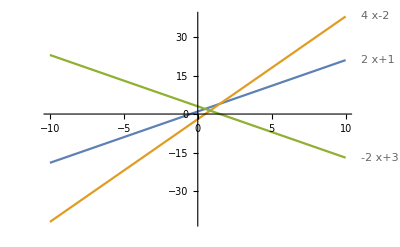

```mathematica
Plot[{2x+1,4x-2,-2x+3}, {x,-10,10},PlotLabels->"Expressions"](* Plotting some functions as example *)
```

### Comprensione guidata del parametro q

Partiamo cercando di capire cosa rappresenta il q della formula nei grafici :

```mathematica
Manipulate[Plot[2*x+ q ,{x,-3, +3},PlotLabel-> 2x+q],{q, -10,+10}](* Plotting an example, TODO: Check if zoom function is correct *)
```

```mathematica
hyperText["Hai dubbi su come cambia il grafico quando cambia q?","Il termine noto q indica l’ordinata del punto di intersezione del grafico con l’asse Y",LinkHand] (* Creating a cliccable text *)
```

Hai dubbi su come cambia il grafico quando cambia q?

### Comprensione del caso particolare

Hai posto attenzione a cosa succede quando q = 0?

```mathematica
Row[{Hyperlink[StatusArea[Button["Si"], "AG_C1_G1"],{EvaluationNotebook[], "AG_C1_G1"}],"\t",Button["No",If[p1== 0,p1=1;Print[Plot[2x, {x,-5,+5}, PlotLegends->"y = 2 x + 0"]]]]}] (* Generating Button[YES] to proceed and Button[NO] to draw the answer *)
```

No

### Analisi guidata del coefficiente di primo grado

Ora abbiamo capito cosa vuol dire il termine noto sul grafico ma il coefficiente di primo grado m come si traduce sul grafico?

```mathematica
Manipulate[Plot[m*x-2 ,{x,-3, +3},PlotLabel-> m *x-2],{m, -10,+10}]
```

```mathematica
EventHandler[MouseAppearance[Style["Hai dubbi su come cambia il grafico quando cambia m?” ",FontColor->Blue],LinkHand],{"MouseClicked":>  MessageDialog["Il coefficiente di primo grado indica l’inclinazione del grafico rispetto all’asse X"]}]
```

Hai dubbi su come cambia il grafico quando cambia m?”

### Comprensione del caso particolare

Hai notato cosa cambia se m < 0 o m > 0?

Si	No

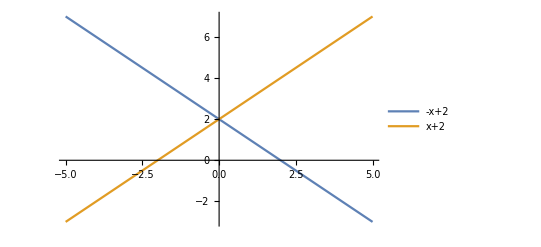

Come puoi vedere i grafici formano con l’asse x angoli acuti se m>0 e ottusi se m<0

```mathematica
Row[{Button["Si"],"\t",Button["No",If[p2 == 0,p2=1;Print[Plot[{-x+2,x+2}, {x,-5,+5}, PlotLegends->"Expressions"]]; Print["Come puoi vedere i grafici formano con l’asse X angoli acuti se m>0 e ottusi se m<0"],p2=1]]}]
```

### Comprensione del caso particolare

Hai notato cosa succede se m = 0?

Si	No

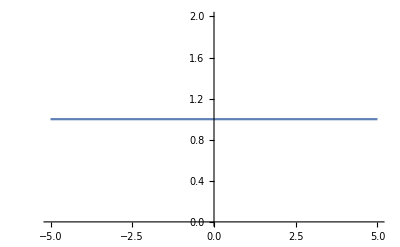

Come puoi vedere il grafico è parallelo all'asse X

```mathematica
Row[{Button["Si" ],"\t",Button["No",If[p3 == 0,p3=1;Print[Plot[0x+1, {x,-5,+5}, PlotLegends->"Expressions"]]; Print["Come puoi vedere il grafico è parallelo all'asse X"],p3=1]]}]
```

### Caso particolare x=k

Prima di farti sperimentare liberamente bisogna riflettere su un caso unico delle rette non delle funzioni.
Pensa a quale possa essere e poi scopriamolo insieme.


Il caso delle rette verticali che sono della forma x=k con k che è un qualunque numero.

```mathematica
Manipulate[ListLinePlot[{{k,10},{k,-10}},PlotRange->{{-4,+4},{-4,+4}},PlotLabel->StringJoin["x = ",ToString[k]]],{k,-3.5,3.5}]
```

### Ora tocca a te!

Inserisci tu le rette e osserva come sono rappresentate graficamente. Puoi confrontare contemporaneamente 5 funzioni polinomiali.

```mathematica
freeEq = {}(* List that contains at most 5 expressions to be compared, TODO: Insert in package*)
```

{}

```mathematica
currentEq ="" (* Current expression that user is inserting, TODO: Insert in package *)
```

```mathematica
Dynamic[freeEq] (* DEBUG *)
```

```mathematica
Panel[Column[{
Row[{InputField[Dynamic[currentEq],String],Button["Confronta",If[Length[freeEq]<5,AppendTo[freeEq,ToExpression[currentEq]],MessageDialog["Hai già inserito 5 grafici, eliminane uno prima di aggiungerne uno nuovo!"]]]}],Dynamic[Row[Table[With[{i=i},Column[{Plot[freeEq[[i]],{x,-10,+10},PlotLabel->ToString[freeEq[[i]]],ImageSize->Small],"\t",Button["Elimina",freeEq=Delete[freeEq,Position[freeEq,freeEq[[i]]]]]}]],{i,Length[freeEq]}]]]}]](* Drawing the list of the functions that the user want to compare, Delete button allow to remove that expression from the list; TODO Insert in package *)
```

Confronta

```mathematica
Row[{Hyperlink[StatusArea[Button["Ti senti pronto per gli esercizi"], "ES_G1"],{EvaluationNotebook[], "ES_G1"}]}]
```

### Esercizi Tipologia 1

```mathematica
Dynamic[teacherEQ](* DEBUG *)
```

```mathematica
Dynamic[exercises](* DEBUG *)
```

```mathematica
exKindAPrinter[1]
```

A quale funzione corrisponde la seguente retta?
Zoom sugli zeri:1

Reset Zoom

A quale funzione corrisponde la seguente retta?
Zoom sugli zeri:1

Reset Zoom

A quale funzione corrisponde la seguente retta?
Zoom sugli zeri:1

Reset Zoom

```mathematica
clicked = 0
```

0

```mathematica
Dynamic[Button["Verifica",If[userAnswer[[1,1]] ===   0  || userAnswer[[1,2]] === 0 || userAnswer[[1,3]] ===  0,  MessageDialog["Rispondi a tutte le domande prima di verificare"] , checkAnswer[1]; clicked =1] ]]
```

```mathematica
Dynamic[If[clicked === 1,Hyperlink[StatusArea[Button["Vai alla prossima sezione"],"ES_G1_B"],{EvaluationNotebook[], "ES_G1_B"}], "Verifica la risposta prima di passare alla prossima sezione"]]
```

```mathematica
Dynamic[correctCounter]
```

### Esercizi Tipologia 2

```mathematica
exKindBPrinter[2]
```

Zoom sugli zeri:1

Reset ZoomZoom sugli zeri:1

Reset ZoomZoom sugli zeri:1

Reset ZoomZoom sugli zeri:1

Reset Zoom

Zoom sugli zeri:1

Reset ZoomZoom sugli zeri:1

Reset ZoomZoom sugli zeri:1

Reset ZoomZoom sugli zeri:1

Reset Zoom

Zoom sugli zeri:1

Reset ZoomZoom sugli zeri:1

Reset ZoomZoom sugli zeri:1

Reset ZoomZoom sugli zeri:1

Reset Zoom

```mathematica
clicked1b = 0
```

0

```mathematica
Dynamic[Button["Verifica",If[userAnswer[[2,1]] ===   0  || userAnswer[[2,2]] === 0 || userAnswer[[2,3]] ===  0,  MessageDialog["Rispondi a tutte le domande prima di verificare"] , checkAnswer[2]; clicked1b =1] ]]
```

```mathematica
Dynamic[If[clicked1b=== 1,Hyperlink[StatusArea[Button["Vai alla prossima sezione"],"RS1"],{EvaluationNotebook[], "RS1"}], "Verifica la risposta prima di passare alla prossima sezione"]]
```

## Risultati

```mathematica
correctAnswerG1 =  correctCounter(*sarà uguale alla correctAnswer in questo momento cosi da salvare il numero di risposte esatte al primo step*)
```

0

```mathematica
Dynamic[correctCounter]
```

```mathematica
If[correctAnswerG1  < 4, 
StringForm["Su 6 domande hai risposto correttamente a ``.",correctAnswerG1]
Text["volendo puoi proseguire ma sarebbe meglio ripassare un po di teoria e poi riprovare gli esercizi"]
,
StringForm["Su 6 domande hai risposto correttamente a ``.",correctAnswerG1]
Text["hai compreso bene l’argomento ora puoi proseguire, ma se hai ancora qualche dubbio puoi comunque tornare indietro e riguardare le equazioni di primo grado"]
,
Text["Qualcosa è andato storto!!"]
]
Row[{Hyperlink[StatusArea[Button["Torna alla teoria"], "E_G1"],{EvaluationNotebook[], "E_G1"}]}]
Row[{Hyperlink[StatusArea[Button["Torna all' indice"], "Index"],{EvaluationNotebook[], "Index"}]}] (*in questi due casi caso si chiama lu funzione che resetta i vettori nel package*)
Button["Ricarica Esercizi", resetGrade[1, correctAnswerG1]; NotebookLocate["ES_G1"]](*in questi due casi caso si chiama lu funzione che resetta i vettori nel package*)
Row[{Hyperlink[StatusArea[Button["Sezione Successiva"], "E_2G"],{EvaluationNotebook[], "E_2G"}]}]
```

Su 6 domande hai risposto correttamente a 0. volendo puoi proseguire ma sarebbe meglio ripassare un po di teoria e poi riprovare gli esercizi

Ricarica Esercizi

Funzioni polinomiali di 2 °Grado

### Introduzione

Le funzioni polinomiali di secondo grado hanno la forma y=ax^2+bx+c ovvero una parabola ma cosa vogliono dire i parametri a, b e c?

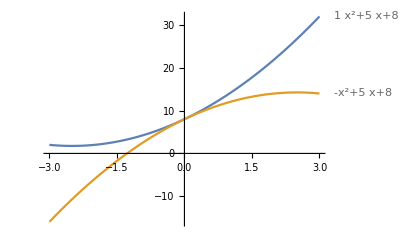

```mathematica
Plot[{1*x^2+5*x + 8, -1*x^2+5*x + 8 },{x,-3, +3}, PlotLabels-> "Expressions"]
```

### Comprensione guidata del parametro c

Partiamo cercando di capire cosa rappresenta il c della formula:

```mathematica
Manipulate[Plot[x^2+ 2*x+ c,{x,-3, +3}, PlotLabel-> x^2+ 2*x+ c],{c, -10,+10}](* Plotting an example *)
```

```mathematica
hyperText["Hai dubbi su come cambia il grafico quando cambia c?","il termine noto c indica l’ordinata del punto di intersezione del grafico con l’asse Y",LinkHand]
```

Hai dubbi su come cambia il grafico quando cambia c?

### Comprensione del caso particolare

Hai posto attenzione a cosa succede quando c=0?

```mathematica
p1 = 0
```

0

```mathematica
Row[{Hyperlink[StatusArea[Button["Si"], "CG_G2_PB"],{EvaluationNotebook[], "CG_G2_PB"}],"\t",Button["No",If[p1== 0,p1=1;Print[Plot[x^2 +  2x, {x,-5,+5}, PlotLegends->"y = x^2 + 2x"]]; Print["Come puoi vedere il grafico passa per l' origine"]]]}]
```

No

### Comprensione guidata del parametro b

Ma il parametro b come si traduce sul grafico?

```mathematica
Manipulate[Plot[x^2+ b*x - 1,{x,-3, +3}, PlotLabel-> x^2+ b*x- 1],{b, -10,+10}]
```

```mathematica
hyperText["Hai dubbi su come cambia il grafico quando cambia b?","il coefficiente del termine di primo grado della X ha segno opposto ed e’ il doppio dell’ascissa del vertice della parabola",LinkHand]
```

Hai dubbi su come cambia il grafico quando cambia b?

### Comprensione del caso particolare

Hai posto attenzione a cosa succede quando b=0?

```mathematica
p2 = 0
```

0

```mathematica
Row[{Hyperlink[StatusArea[Button["Si"], "CG_G2_PB"],{EvaluationNotebook[], "CG_G2_PB"}],"\t",Button["No",If[p2== 0,p2=1;Print[Plot[x^2 +  1, {x,-5,+5}, PlotLegends->"y = x^2 + 1"]]; Print["come puoi vedere il grafico ha vertice sull’asse Y"]]]}]
```

No

### Comprensione guidata del parametro a

cosa vuol dire graficamente il coefficiente a?

```mathematica
Manipulate[Plot[a*x^2 - 2*x  + 1,{x,-3, +3},PlotLabel->a* x^2 - 2*x + 1],{a, -10,+10}]
```

```mathematica
hyperText["Hai dubbi su come cambia il grafico quando cambia a?","il coefficiente del termine di secondo grado della X se positivo mi indica che la parabola e’ rivolta verso l’alto mentre se negativa e’ rivolta verso il basso.",LinkHand]
```

Hai dubbi su come cambia il grafico quando cambia a?

### Caso particolare a = 0

Hai posto attenzione a cosa succede quando a=0?

```mathematica
p3 = 0
```

0

```mathematica
Row[{Hyperlink[StatusArea[Button["Si"], "TS2"],{EvaluationNotebook[], "TS2"}],"\t",Button["No",If[p3== 0,p3=1;Print[Plot[- 2x + 1, {x,-5,+5}, PlotLegends->"y = -2x + 1"]]; Print["come puoi vedere il grafico non e’ piu’ una parabola ma degenera in una retta"]]]}]
```

No

### Ora tocca a te!

Inserisci tu le parabole e osserva come sono rappresentate graficamente.Puoi confrontare contemporaneamente 5 equazioni

```mathematica
freeEq2 = {}
currentEq2=""
Panel[Column[{
Row[{InputField[Dynamic[currentEq2],String],Button["Confronta",If[Length[freeEq2]<5,AppendTo[freeEq2,ToExpression[currentEq2]],MessageDialog["Hai già inserito 5 grafici, eliminane uno prima di aggiungerne uno nuovo!"]]]}],Dynamic[Row[Table[With[{i=i},Column[{Plot[freeEq2[[i]],{x,-10,+10},PlotLabel->ToString[freeEq2[[i]]],ImageSize->Small],"\t",Button["Elimina",freeEq2=Delete[freeEq2,Position[freeEq2,freeEq2[[i]]]]]}]],{i,Length[freeEq2]}]]]}]](* Drawing the list of the functions that the user want to compare, Delete button allow to remove that expression from the list; TODO Insert in package *)
```

{}

Confronta

```mathematica
Row[{Hyperlink[StatusArea[Button["Ti senti pronto per gli esercizi ?"], "ES_G2"],{EvaluationNotebook[], "ES_G2"}]}]
```

### Esercizi Tipologia 1

```mathematica
exKindAPrinter[3]
```

A quale funzione corrisponde la seguente retta?
Zoom sugli zeri:

Reset Zoom

A quale funzione corrisponde la seguente retta?
Zoom sugli zeri:12

Reset Zoom

A quale funzione corrisponde la seguente retta?
Zoom sugli zeri:12

Reset Zoom

```mathematica
clicked2 = 0;
Dynamic[Button["Verifica",If[userAnswer[[3,1]] ===   0  || userAnswer[[3,2]] === 0 || userAnswer[[3,3]] ===  0,  MessageDialog["Rispondi a tutte le domande prima di verificare"] , checkAnswer[3]; clicked2 =1] ]]
Dynamic[If[clicked2=== 1,Hyperlink[StatusArea[Button["Vai alla prossima sezione"],"ES_G2_B"],{EvaluationNotebook[], "ES_G2_B"}], "Verifica la risposta prima di passare alla prossima sezione"]]
```

### Esercizi Tipologia 2

```mathematica
exKindBPrinter[4]
```

Zoom sugli zeri:12

Reset ZoomZoom sugli zeri:12

Reset ZoomZoom sugli zeri:

Reset ZoomZoom sugli zeri:12

Reset Zoom

Zoom sugli zeri:12

Reset ZoomZoom sugli zeri:

Reset ZoomZoom sugli zeri:

Reset ZoomZoom sugli zeri:12

Reset Zoom

Zoom sugli zeri:12

Reset ZoomZoom sugli zeri:12

Reset ZoomZoom sugli zeri:

Reset ZoomZoom sugli zeri:12

Reset Zoom

```mathematica
clicked2B = 0;
Dynamic[Button["Verifica",If[userAnswer[[4,1]] ===   0  || userAnswer[[4,2]] === 0 || userAnswer[[4,3]] ===  0,  MessageDialog["Rispondi a tutte le domande prima di verificare"] , checkAnswer[4]; clicked2B =1] ]]
Dynamic[If[clicked2B=== 1,Hyperlink[StatusArea[Button["Vai alla prossima sezione"],"RS_G2"],{EvaluationNotebook[], "RS_G2"}], "Verifica la risposta prima di passare alla prossima sezione"]]
```

### Risultati

```mathematica
correctAnswerG2=  correctCounter - correctAnswerG1;(*In questo caso sara uguale correctAnswer - correctAnswerG1 per contare tutte le risposte esatte per la sezione di grado 2*)
```

```mathematica
If[correctAnswerG2  < 4, 
StringForm["Su 6 domande hai risposto correttamente a ``.",correctAnswerG2]
Text["volendo puoi proseguire ma sarebbe meglio ripassare un po di teoria e poi riprovare gli esercizi"]
,
StringForm["Su 6 domande hai risposto correttamente a ``.",correctAnswerG2]
Text["hai compreso bene l’argomento ora puoi proseguire, ma se hai ancora qualche dubbio puoi comunque tornare indietro e riguardare le equazioni di primo grado"]
,
Text["Qualcosa è andato storto!!"]
]
Row[{Hyperlink[StatusArea[Button["Torna alla teoria"], "E_2G"],{EvaluationNotebook[], "E_2G"}]}]

Row[{Hyperlink[StatusArea[Button["Torna all' indice"], "Index"],{EvaluationNotebook[], "Index"}]}] (*in questi due casi caso si chiama lu funzione che resetta i vettori nel package*)
Button["Ricarica Esercizi", resetGrade[2, correctAnswerG2]; NotebookLocate["ES_G2"]]
(*in questi due casi caso si chiama lu funzione che resetta i vettori nel package*)
Row[{Hyperlink[StatusArea[Button["Sezione Successiva"], "E_G3"],{EvaluationNotebook[], "E_G3"}]}]
```

Su 6 domande hai risposto correttamente a 0. volendo puoi proseguire ma sarebbe meglio ripassare un po di teoria e poi riprovare gli esercizi

Ricarica Esercizi

Funzioni polinomiali di 3 °Grado

### Introduzione

Le funzioni polinomiali di terzo grado hanno la forma y=ax^2+bx^2+cx+d ovvero una cubica ma cosa vogliono dire i parametri a, b, c e d?

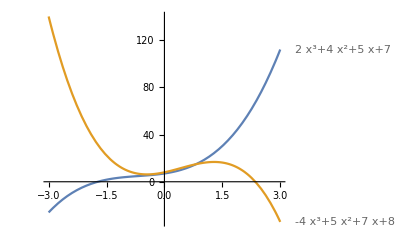

```mathematica
Plot[{2*x^3+4*x ^2+5*x+ 7,-4*x^3+5*x^2+7*x+ 8},{x,-3, +3}, PlotLabels-> "Expressions"]
```

### Comprensione guidata del parametro d

Partiamo cercando di capire cosa rappresenta il d della formula

```mathematica
Manipulate[Plot[2*x^3 +3*x^2+ x+ d,{x,-3, +3}, PlotLabel->x^3 + x^2+ 2*x+ d],{d, -10,+10}](* Plotting an example *)
```

```mathematica
hyperText["Hai dubbi su come cambia il grafico quando cambia d?","il termine noto c indica l’ordinata del punto di intersezione del grafico con l’asse Y",LinkHand]
```

Hai dubbi su come cambia il grafico quando cambia d?

### Caso particolare d = 0

Hai posto attenzione a cosa succede quando d=0?

```mathematica
p4= 0
Row[{Hyperlink[StatusArea[Button["Si"], "E_G3_CC"],{EvaluationNotebook[], "E_G3_CC"}],"\t",Button["No",If[p4== 0,p4=1;Print[Plot[2*x^3 +3*x^2+ x, {x,-5,+5}, PlotLegends->"y = 2*x^3 +3*x^2+ x"]]; Print["come puoi vedere il grafico passa  per l’origine"]]]}]
```

0

No

### Comprensione guidata del parametro c

Ma il parametro c come si traduce sul grafico?

```mathematica
Manipulate[Plot[2*x^3 +3*x^2+ c*x+ 1,{x,-3, +3}, PlotLabel->2*x^3 +3*x^2+ c*x+ 1],{c, -10,+10}]
```

```mathematica
hyperText["Hai dubbi su come cambia il grafico quando cambia c?","il coefficiente del termine di primo grado della X più è grande più indica quanto il grafico assomiglia a una retta",LinkHand]
```

Hai dubbi su come cambia il grafico quando cambia c?

### Comprensione guidata parametro b

Ma il parametro b come si traduce sul grafico?

```mathematica
Manipulate[Plot[2*x^3 +b*x^2+ x+ 1,{x,-3, +3}, PlotLabel->x^3 + b * x^2+ x+ 1],{b, -10,+10}]
```

```mathematica
hyperText["Hai dubbi su come cambia il grafico quando cambia b?","il coefficiente del termine di secondo grado della X più è grande più indica quanto il grafico nei suoi rami assomiglia a una parabola",LinkHand]
```

Hai dubbi su come cambia il grafico quando cambia b?

### Comprensione guidata parametro a

cosa vuol dire graficamente il coefficiente a?

```mathematica
Manipulate[Plot[a*x^3 +4*x^2+ x+ 1,{x,-3, +3},PlotLabel->a* x^3 + 4* x^2+ x+ 1],{a, -10,+10}]
```

```mathematica
hyperText["Hai dubbi su come cambia il grafico quando cambia a?","il coefficiente del termine di terzo grado della X indica quanto il grafico è pendente",LinkHand]
```

Hai dubbi su come cambia il grafico quando cambia a?

### Caso particolare

Hai notato cosa cambia se a<0 o a>0?

```mathematica
p5= 0
Row[{Hyperlink[StatusArea[Button["Si"], "E3_CP_A0"],{EvaluationNotebook[], "E3_CP_A0"}],"\t",Button["No",If[p5== 0,p5=1;Print[Plot[{x^3 + 4*x^2+ x + 1, - x^3 + 4*x^2+ x + 1}, {x,-5,+5}, PlotLabels-> "Expressions"]]; Print["come puoi vedere dai grafici se a>0 allora il grafico cresce al crescere delle X, se a<0 il grafico decresce al decrescere delle X"]]]}]
```

0

No

### Caso particolare a = 0

Hai posto attenzione a cosa succede quando a=0?

```mathematica
p6= 0
Row[{Hyperlink[StatusArea[Button["Si"], "E3_CP_A0"],{EvaluationNotebook[], "E3_CP_A0"}],"\t",Button["No",If[p6== 0,p6=1;Print[Plot[0*x^3 + 4*x^2+ x + 1, {x,-5,+5}, PlotLegends-> " 0*x^3 + 4*x^2+ x + 1"]]; Print["come puoi vedere il grafico non e’ piu’ una cubica ma degenera in una parabola"]]]}]
```

0

No

### Comprensione degli zeri

Per capire quante volte la curva interseca l’asse X e quindi quanti rami diversi di curva possediamo dobbiamo scoprire quanti risultati ha l’equazione 0=ax3+bx2+cx+d, dobbiamo considerare anche la molteplicità con cui compaiono

1° grafico deve comparire quando zumma sempre: “zero di molteplicità 1”
2° grafico deve comparire quando zumma sul primo zero: “zero di molteplicità 1”, sul secondo zoom: “zero di molteplicità 2”
3° grafico deve comparire quando zumma: “zero di molteplicità 3”

```mathematica
plotWithZoomButtons[x^3 +3 x^2+ 4x, Symbol["x"]]
plotWithZoomButtons[x^3 +x^2, Symbol["x"]]
plotWithZoomButtons[x^3 +3*x^2+3*x+ 1, Symbol["x"]]
```

-1

0

0

Zoom sugli zeri:1

Reset Zoom

Zoom sugli zeri:12

Reset Zoom

Zoom sugli zeri:1

Reset Zoom

-1

0

0

-1

-1

-1

«4 more identical outputs»

0

-1

### Ora tocca a te!

ora tocca a puoi sperimentare. Inserisci tu le funzioni polinomiali e osserva come sono rappresentate graficamente. Puoi confrontarne contemporaneamente 5.

```mathematica
freeEq3 = {}
currentEq3=""
Panel[Column[{
Row[{InputField[Dynamic[currentEq3],String],Button["Confronta",If[Length[freeEq3]<5,AppendTo[freeEq2,ToExpression[currentEq3]],MessageDialog["Hai già inserito 5 grafici, eliminane uno prima di aggiungerne uno nuovo!"]]]}],Dynamic[Row[Table[With[{i=i},Column[{Plot[freeEq3[[i]],{x,-10,+10},PlotLabel->ToString[freeEq3[[i]]],ImageSize->Small],"\t",Button["Elimina",freeEq3=Delete[freeEq3,Position[freeEq3,freeEq3[[i]]]]]}]],{i,Length[freeEq3]}]]]}]](* Drawing the list of the functions that the user want to compare, Delete button allow to remove that expression from the list; TODO Insert in package *)
```

{}

Confronta

```mathematica
Row[{Hyperlink[StatusArea[Button["Ti senti pronto per gli esercizi"], "ES_G3"],{EvaluationNotebook[], "ES_G3"}]}]
```

### Esercizi Tipologia 1

```mathematica
exKindAPrinter[5]
```

A quale funzione corrisponde la seguente retta?
Zoom sugli zeri:1

Reset Zoom

A quale funzione corrisponde la seguente retta?
Zoom sugli zeri:123

Reset Zoom

A quale funzione corrisponde la seguente retta?
Zoom sugli zeri:1

Reset Zoom

```mathematica
clicked3 = 0;
Dynamic[Button["Verifica",If[userAnswer[[5,1]] ===   0  || userAnswer[[5,2]] === 0 || userAnswer[[5,3]] ===  0,  MessageDialog["Rispondi a tutte le domande prima di verificare"] , checkAnswer[5]; clicked3 =1] ]]
Dynamic[If[clicked3=== 1,Hyperlink[StatusArea[Button["Vai alla prossima sezione"],"ES_G3_B"],{EvaluationNotebook[], "ES_G3_B"}], "Verifica la risposta prima di passare alla prossima sezione"]]
```

### Esercizi Tipologia 2

```mathematica
exKindBPrinter[6]
```

Zoom sugli zeri:1

Reset ZoomZoom sugli zeri:1

Reset ZoomZoom sugli zeri:1

Reset ZoomZoom sugli zeri:1

Reset Zoom

Zoom sugli zeri:1

Reset ZoomZoom sugli zeri:1

Reset ZoomZoom sugli zeri:1

Reset ZoomZoom sugli zeri:1

Reset Zoom

Zoom sugli zeri:1

Reset ZoomZoom sugli zeri:1

Reset ZoomZoom sugli zeri:1

Reset ZoomZoom sugli zeri:1

Reset Zoom

```mathematica
clicked3B = 0;
Dynamic[Button["Verifica",If[userAnswer[[6,1]] ===   0  || userAnswer[[6,2]] === 0 || userAnswer[[6,3]] ===  0,  MessageDialog["Rispondi a tutte le domande prima di verificare"] , checkAnswer[4]; clicked3B =1] ]]
Dynamic[If[clicked3B=== 1,Hyperlink[StatusArea[Button["Vai alla prossima sezione"],"RS_G3"],{EvaluationNotebook[], "RS_G3"}], "Verifica la risposta prima di passare alla prossima sezione"]]
```

### Risultati

```mathematica
correctAnswerG3 = correctCounter - correctAnswerG1 - correctAnswerG2 (*correct Answer total -g1 g2*)
```

0

```mathematica
If[correctAnswerG3  < 4, 
StringForm["Su 6 domande hai risposto correttamente a ``.",correctAnswerG3]
Text["volendo puoi proseguire ma sarebbe meglio ripassare un po di teoria e poi riprovare gli esercizi"]
,
StringForm["Su 6 domande hai risposto correttamente a ``.",correctAnswerG3]
Text["hai compreso bene l’argomento ora puoi proseguire, ma se hai ancora qualche dubbio puoi comunque tornare indietro e riguardare le equazioni di primo grado"]
,
Text["Qualcosa è andato storto!!"]
]
Row[{Hyperlink[StatusArea[Button["Torna alla teoria"], "E_G3"],{EvaluationNotebook[], "E_G3"}]}] (*chiama funzione reset*)
Row[{Hyperlink[StatusArea[Button["Torna all' indice"], "Index"],{EvaluationNotebook[], "Index"}]}] 
Button["Ricarica Esercizi", resetGrade[3, correctAnswerG1]; NotebookLocate["ES_G3"]]
StringForm["Su 18 domande hai risposto correttamente a ``.",correctCounter]
```

Su 6 domande hai risposto correttamente a 0. volendo puoi proseguire ma sarebbe meglio ripassare un po di teoria e poi riprovare gli esercizi

Ricarica Esercizi

Su 18 domande hai risposto correttamente a 0.